```mathematica
3+5
```

8

```mathematica
l={10,20,30,40,50};
```

```mathematica
l
```

{10,20,30,40,50}

```mathematica
m = {{a,b,c}, {d,f,e}}
```

{{a,b,c},{d,f,e}}

```mathematica
l[[1;;5;;2]]
```

{10,30,50}

```mathematica
m//MatrixForm
```

(a | b | c
d | f | e)

```mathematica
m[[2,2]]
```

f

```mathematica
m[[2]]
```

{d,f,e}

```mathematica
m[[2, ;;]]
```

{d,f,e}

```mathematica
m // MatrixForm
```

(a | b | c
d | f | e)

```mathematica
m[[;;, 3]]
```

{c,e}

```mathematica
i=1;
m[[;;, i;;i+1]]//MatrixForm
```

(a | b
d | f)

```mathematica
Table[m[[;;, i;;i+1]], {i,2}]//MatrixForm
```

((a
b) | (d
f)
(b
c) | (f
e))

```mathematica
m//MatrixForm
```

(a | b | c
d | f | e)

```mathematica
m[[;;, ;; ;;2]]
```

{{a,c},{d,e}}

```mathematica
Table
```

Table

```mathematica
Table[i, {i,5}]
```

{1,2,3,4,5}

```mathematica
Table[i^3-1, {i,5}]
```

{0,7,26,63,124}

```mathematica
Table[i^3-1, {i,3, 12}]
```

{26,63,124,215,342,511,728,999,1330,1727}

```mathematica
Table[i^3-1, {i,3, 12, 3}]
```

{26,215,728,1727}

```mathematica
k =Table[i+j, {i,3}, {j,5}]
```

{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8}}

```mathematica
k//MatrixForm
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8)

```mathematica
k[[;;, {2, 4,5}]] //MatrixForm
```

(3 | 5 | 6
4 | 6 | 7
5 | 7 | 8)

```mathematica
Range[2,7]
```

{2,3,4,5,6,7}

```mathematica
Range[2,10,2]
```

{2,4,6,8,10}

```mathematica
Subdivide[0,1,3]
```

{0,1/3,2/3,1}

```mathematica
Sin[1]
```

Sin[1]

```mathematica
Sin[{1,2,34}]
```

```mathematica
{Sin[1],Sin[2],Sin[34]}
```

```mathematica
n=10;
f=Sin;
d=Subdivide[0,1,n];
N[Total[f[d]*1/n]]
```

0.501388

```mathematica
int[f_,n_]:=(d=Subdivide[0,1,n];
N[Total[f[d]*1/n]])
int[f,10]
```

0.501388

```mathematica
diff = Table[Abs[NIntegrate[f[x],{x,0,1}] - int[f,i]], {i,2,20}]
```

{0.200751,0.135981,0.102787,0.0826138,0.069058,0.059323,0.0519932,0.0462754,0.0416904,0.037932,0.0347952,0.0321376,0.0298571,0.0278788,0.0261463,0.0246166,0.023256,0.0220379,0.020941}

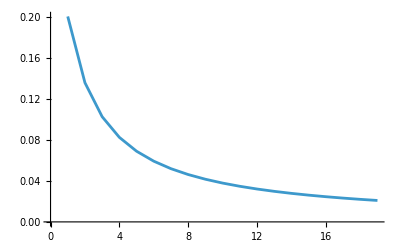

```mathematica
ListLinePlot[diff]
```

```mathematica
v1={a,b,c};
v2={1,2,3};
```

```mathematica
v1+v2
```

{1+a,2+b,3+c}

```mathematica
v1.v2
```

```mathematica
a+2 b+3 c
```

```mathematica
Norm[v2,17]
```

2^(2/17) 32317809^(1/17)

```mathematica
ml={{u,v}, {w,q}}
```

{{u,v},{w,q}}

```mathematica
Det[ml]
```

q u-v w

```mathematica
Tr[ml]
```

q+u

```mathematica
Transpose[ml]
```

{{u,w},{v,q}}

```mathematica
m2={{1,2}, {112,7}}
```

{{1,2},{112,7}}

```mathematica
MatrixRank[m2]
```

2

```mathematica
ml.m2
```

{{u+112 v,2 u+7 v},{112 q+w,7 q+2 w}}

```mathematica
ml.m2 //MatrixForm
```

(u+112 v | 2 u+7 v
112 q+w | 7 q+2 w)

```mathematica
Inverse[ml]
```

{{q/(q u-v w),-v/(q u-v w)},{-w/(q u-v w),u/(q u-v w)}}

```mathematica
Inverse[ml].ml ==IdentityMatrix[2]//MatrixForm
```

{{(q u)/(q u-v w)-(v w)/(q u-v w),0},{0,(q u)/(q u-v w)-(v w)/(q u-v w)}}=={{1,0},{0,1}}

```mathematica
Simplify[Inverse[ml].ml ==IdentityMatrix[2]]
```

True

```mathematica
CharacteristicPolynomial
```

CharacteristicPolynomial

```mathematica
CharacteristicPolynomial[ml,t]
```

-q t+t^2+q u-t u-v w

```mathematica
ml
```

{{u,v},{w,q}}

```mathematica
Eigenvalues[m2]
```

{4+√233,4-√233}

```mathematica
Eigenvectors[m2]
```

{{1/112 (-3+√233),1},{1/112 (-3-√233),1}}

```mathematica
RowReduce[m2]
```

{{1,0},{0,1}}

```mathematica
RowReduce[{{1,2,a},{1,3,b}}]
```

{{1,0,3 a-2 b},{0,1,-a+b}}

```mathematica
RowReduce[{{1,2,a},{1,3,b}}]//MatrixForm
```

(1 | 0 | 3 a-2 b
0 | 1 | -a+b)

```mathematica
NullSpace[m2]
```

{}

```mathematica
NullSpace[{{1,0,0}, {0,0,0}, {0,0,0}}]
```

{{0,0,1},{0,1,0}}

```mathematica
NullSpace[Partition[Range[9],3]]
```

{{1,-2,1}}

```mathematica
Sqrt[x^2]
```

√(x^2)

```mathematica
x>=0
```

x≥0

```mathematica
Refine[Sqrt[x^2], x>=0]
```

x

```mathematica
z*Gamma[z]
```

z Gamma[z]

```mathematica
FullSimplify[z*Gamma[z]]
```

Gamma[1+z]

```mathematica
Simplify[ArcCos[Cos[x]], 0<=x<=Pi]
```

x

```mathematica
FullSimplify[x*Gamma[x]]
```

Gamma[1+x]

```mathematica
FullSimplify[x*Gamma[x], Element[x, Integers]&& x>= 0]
```

x!

```mathematica
r1 = Expand[(x+y)*(x^3+y^2+z)]
```

x^4+x^3 y+x y^2+y^3+x z+y z

```mathematica
Expand[Cos[2*x]]
```

Cos[2 x]

```mathematica
Expand[Cos[2*x], Trig->True]
```

Cos[x]^2-Sin[x]^2

```mathematica
Factor[r1]
```

(x+y) (x^3+y^2+z)

```mathematica
Factor[Cos[x]-Cos[y], Trig->True]
```

-2 Sin[x/2-y/2] Sin[x/2+y/2]

```mathematica
e1 =1/x +(1+x)/(x^2+x)
```

1/x+(1+x)/(x+x^2)

```mathematica
Together[e1]
```

2/x

```mathematica
Apart[e1]
```

2/x

```mathematica
Apart[(-8-5*x^2+12*x^3-x^4+2*x^5)/((1+x)^2*(1+x^2)^2)]
```

-7/(1+x)^2+1/(1+x)+(-5+2 x)/((1+x^2)^2)+(3+x)/(1+x^2)

```mathematica
FullSimplify[Log[Exp[x]],x>0]
```

x

```mathematica
Sin[Pi*x+Pi*3/2]*Cos[Pi*x/2]
```

-Cos[(π x)/2] Cos[π x]

```mathematica
FullSimplify[Sin[Pi*x+Pi*3/2]*Cos[Pi*x/2],Element[x,Integers]&&Mod[x,2]==0]
```

-ⅈ^x

```mathematica
e3=(a||b&&(a||!c))&&(b||c&&(b||!a))&&(a||c&&(a||!b))
```

(a||(b&&(a||!c)))&&(b||(c&&(b||!a)))&&(a||(c&&(a||!b)))

```mathematica
FullSimplify[e3]
```

a&&b

```mathematica
m=.
m[a,b]
ForAll[{a,b,c}, m[a,m[b,c]]==m[m[a,b],c]]
```

m[a,b]

∀_{a,b,c}m[a,m[b,c]]==m[m[a,b],c]

```mathematica
d=.
```

```mathematica
ForAll[{a,b,c,d},m[a,m[b,m[c,d]]]==m[a,m[m[b,c],d]]==m[m[a,b],m[c,d]]]
```

∀_{a,b,c,d}m[a,m[b,m[c,d]]]==m[a,m[m[b,c],d]]==m[m[a,b],m[c,d]]